```mathematica
SetDirectory["G:\\My Drive\\Projects\\FourierDisplay\\Software"];
LoadPack:=Get["G:\\My Drive\\Projects\\FourierDisplay\\Software\\FourierPack.wl"];
LoadPack;
```

## Test Data

```mathematica
LinSpace[n_,{a_,b_}]:=Array[#&,n,{a,b}];
```

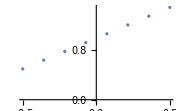

```mathematica
testData[1] =Table[ReIm[x+(x+1)*ⅈ],{x,LinSpace[8,{-.5,.5}]}];
ListPlot[testData[1], ImageSize->Small]
```

```mathematica
testData[2] = Table[ReIm[Sin[x]*ⅈ+Cos[x]], {x,LinSpace[8,π/4+π/16*{-1,1}]}];
```

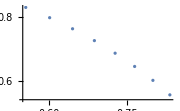

```mathematica
ListPlot[testData[2], ImageSize->Small]
```

## Magnitudes

```mathematica
P[N_]:=Module[{p},p/.FindRoot[p^(N+1)-2p+1==0,{p,0.5}]]
```

```mathematica
M[i_, N_, M0_]:=P[N]^i*M0;
M[0,N_,M0_]:=M0;
$M[i_,N_]:=M[i,N,1];
$MTable[N_]:=Table[M[i,N,1],{i,0,N-1}]
```

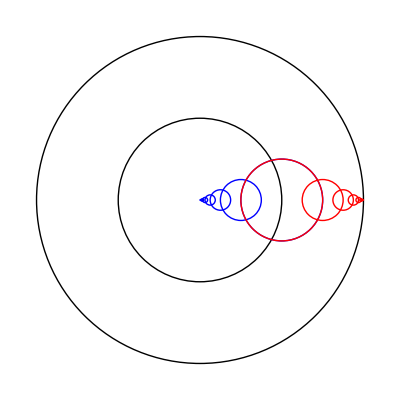

```mathematica
With[{M = $MTable[10]},
Graphics[
{Circle[{0,0},First@M],
Circle[{0,0},Total@M],
Blue,MapThread[Circle[{#1,0}, #2]&,{Most@FoldList[Subtract,M],Rest@M}],
Red,MapThread[Circle[{#1,0}, #2]&,{Most@FoldList[Plus,M],Rest@M}]
}
]]
```

## Functions and Model

```mathematica
FHat[N_, M_, θ_]:=Sum[M[i]*Exp[ⅈ*θ[i]], {i,0,N}];
FHat[N_, M_, ω_, ϕ_,t_]:=Sum[M[i]*Exp[ⅈ*(ω[i]*t+ϕ[i])], {i,0,N}];
```

```mathematica
FHat[3,$M[#,3]&,θ]
```

ⅇ^(ⅈ θ[0])+0.543689 ⅇ^(ⅈ θ[1])+0.295598 ⅇ^(ⅈ θ[2])+0.160713 ⅇ^(ⅈ θ[3])

```mathematica
FindInstance[1*ⅈ==FHat[3,$M[#,3]&,θ], Table[θ[i],{i,0,3}]]
```

{{θ[0]→0.972414-2.20395 ⅈ,θ[1]→-1/10-(9 ⅈ)/10,θ[2]→-23/10-(17 ⅈ)/5,θ[3]→27/10-(13 ⅈ)/10}}

## NonlinearModelFit - Direct

ⅇ^(ⅈ (ϕ[0]+t ω[0]))+0.543689 ⅇ^(ⅈ (ϕ[1]+t ω[1]))+0.295598 ⅇ^(ⅈ (ϕ[2]+t ω[2]))+0.160713 ⅇ^(ⅈ (ϕ[3]+t ω[3]))

FindFit::nrnum: The function value √(Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«1»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2+Abs[Re[($model+Times[«2»]) (Conjugate[«1»]+Times[«2»])]]^2) is not a real number at {ω[0],ϕ[0],ω[1],ϕ[1],ω[2],ϕ[2],ω[3],ϕ[3],ω[4],ϕ[4]} = {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}.

ReplaceAll::reps: {FindFit[{{Cos[(3 π)/16],Sin[(3 π)/16]},{Cos[(23 π)/112],Sin[(23 π)/112]},{Cos[(25 π)/112],Sin[(25 π)/112]},{Cos[(27 π)/112],Sin[(27 π)/112]},{Sin[(27 π)/112],Cos[(27 π)/112]},{Sin[(25 π)/112],Cos[(25 π)/112]},{Sin[(23 π)/112],Cos[(23 π)/112]},{Sin[(3 π)/16],Cos[(3 π)/16]}},$model,{ω[0],ϕ[0],ω[1],ϕ[1],ω[2],ϕ[2],ω[3],ϕ[3],ω[4],ϕ[4]},t,NormFunction→(Norm[Re[Slot[«1»] Conjugate[«1»]]]&)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ⅇ^(ⅈ (ϕ[0]+t ω[0]))+0.543689 ⅇ^(ⅈ (ϕ[1]+t ω[1]))+0.295598 ⅇ^(ⅈ (ϕ[2]+t ω[2]))+0.160713 ⅇ^(ⅈ (ϕ[3]+t ω[3]))/.FindFit[{{Cos[(3 π)/16],Sin[(3 π)/16]},{Cos[(23 π)/112],Sin[(23 π)/112]},{Cos[(25 π)/112],Sin[(25 π)/112]},{Cos[(27 π)/112],Sin[(27 π)/112]},{Sin[(27 π)/112],Cos[(27 π)/112]},{Sin[(25 π)/112],Cos[(25 π)/112]},{Sin[(23 π)/112],Cos[(23 π)/112]},{Sin[(3 π)/16],Cos[(3 π)/16]}},$model,{ω[0],ϕ[0],ω[1],ϕ[1],ω[2],ϕ[2],ω[3],ϕ[3],ω[4],ϕ[4]},t,NormFunction→(Norm[Re[#1 Conjugate[#1]]]&)]

General::ivar: 1.00014 is not a valid variable.

ReplaceAll::reps: {FindFit[{{Cos[(3 π)/16],Sin[(3 π)/16]},{Cos[(23 π)/112],Sin[(23 π)/112]},{Cos[(25 π)/112],Sin[(25 π)/112]},{Cos[(27 π)/112],Sin[(27 π)/112]},{Sin[(27 π)/112],Cos[(27 π)/112]},{Sin[(25 π)/112],Cos[(25 π)/112]},{Sin[(23 π)/112],Cos[(23 π)/112]},{Sin[(3 π)/16],Cos[(3 π)/16]}},$model,{ω[0],ϕ[0],ω[1],ϕ[1],ω[2],ϕ[2],ω[3],ϕ[3],ω[4],ϕ[4]},1.00014,NormFunction→(Norm[Re[Slot[«1»] Conjugate[«1»]]]&)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 1.00014 is not a valid variable.

ReplaceAll::reps: {FindFit[{{Cos[(3 π)/16],Sin[(3 π)/16]},{Cos[(23 π)/112],Sin[(23 π)/112]},{Cos[(25 π)/112],Sin[(25 π)/112]},{Cos[(27 π)/112],Sin[(27 π)/112]},{Sin[(27 π)/112],Cos[(27 π)/112]},{Sin[(25 π)/112],Cos[(25 π)/112]},{Sin[(23 π)/112],Cos[(23 π)/112]},{Sin[(3 π)/16],Cos[(3 π)/16]}},$model,{ω[0],ϕ[0],ω[1],ϕ[1],ω[2],ϕ[2],ω[3],ϕ[3],ω[4],ϕ[4]},1.00014,NormFunction→(Norm[Re[Slot[«1»] Conjugate[«1»]]]&)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 1.00014 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

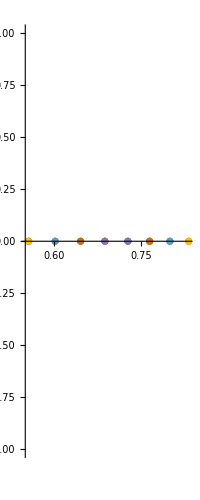

```mathematica
Module[{sols, model, function, test},
test = 2;
model = FHat[3,$M[#,3]&,ω, ϕ,t];
Echo[model];
sols = FindFit[testData[test],$model,Flatten[Table[{ω[i],ϕ[i]},{i,0,4}]],t, NormFunction->(Norm[Re[#*Conjugate[#]]]&)];
function = model/.sols;
Echo[function];
Show[{ComplexListPlot[testData[test]],ParametricPlot[{Re@function, Im@function},{t,1,8}]}]
]
```

## NonlinearModelFit - Term-by-Term

## Binning FFT Results (Come Back to This)

```mathematica
PrepareSample[lineData_,samplesTarget_, scaleTarget_:1]:= Module[{points},
points = lineData/(Mean[Norm/@lineData]*scaleTarget);
(*tour = MakeTour[points]; For some reason Tour isn't playing nice with UniformResample*)
sample = UniformResample[PrependIndices[points, "ParametrizationType"->"EuclidianDistance"],samplesTarget, "ParametrizationType"->"Linear"];
(*Resample with distance along path parametrization, but attach 'linear' (ie 0-N) indices in sample["SamplePointsIndexed"]*)
Return[sample];
];
```

```mathematica
sample = PrepareSample[LineData["VirginiaV"], 100];
```

```mathematica
{approxInfo, approxInfoBinned} = 
Module[{coefObject, numTerms, fmags},
numTerms = 5;
fmags = $MTable[numTerms];
coefObject = CnFFT[MakeComplex[sample["SamplePoints"]], numTerms];ApproxFunction[coefObject["CoefficientFunction"],t,Length@sample["SamplePoints"],coefObject["CoefficientList"], "Sort"->False, "ForcedMagnitudes"->#]&/@{None,fmags}];
{func, funcBinned} = Function[t,Evaluate[#["Function"]]]&/@{approxInfo, approxInfoBinned};
```

```mathematica
EvaluateCircles[sample_, func_]:=
With[{l2 = L2Error[sample["SamplePointsIndexed"], func, "Complex"]},
Column[{
Style[StringForm["L^2 Error = ``",NumberForm[l2["L2Error"],4]],"Text"],
Show[
ListPlot[sample["SamplePoints"]],
ListPlot[l2["ApproxPoints"],PlotStyle->Red], 
ParametricPlot[{Re@#, Im@#}&@func[t],{t,0,sample["Length"]}], ImageSize->Medium]},Center]];
```

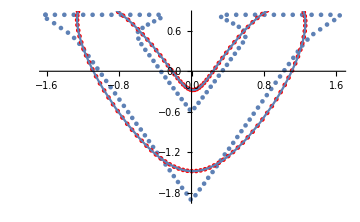
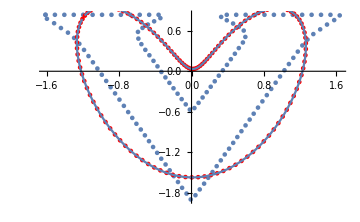
L^2 Error = 0.03905
-Graphics-L^2 Error = 0.06703
-Graphics-

```mathematica
Row[EvaluateCircles[sample,#]&/@{func,funcBinned}]
```

### Binning with Other Line Data

```mathematica
BinAnalysis[data_, MTable_Symbol, numTerms_, numSamples_:100]:=
Module[{sample,approxInfo, approxInfoBinned, func, funcBinned},
sample = PrepareSample[data , numSamples];
{approxInfo, approxInfoBinned} = 
Module[{coefObject, fmags},
fmags = MTable[numTerms];
coefObject = CnFFT[MakeComplex[sample["SamplePoints"]], numTerms];ApproxFunction[coefObject["CoefficientFunction"],t,Length@sample["SamplePoints"],coefObject["CoefficientList"], "Sort"->False, "ForcedMagnitudes"->#]&/@{None,fmags}];
{func, funcBinned} = Function[t,Evaluate[#["Function"]]]&/@{approxInfo, approxInfoBinned};
Grid[{Text@Style[#,Bold]&/@{"Natural", "Binned"},EvaluateCircles[sample,#]&/@{func,funcBinned}}]];
```

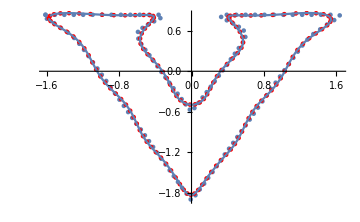
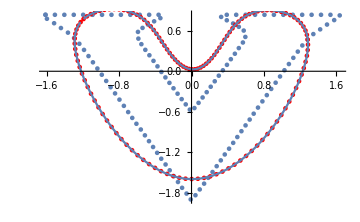
Natural | Binned
L^2 Error = 0.001068
-Graphics- | L^2 Error = 0.06061
-Graphics-

```mathematica
BinAnalysis[LineData["VirginiaV"],$MTable, 20]
```

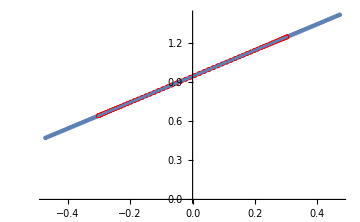
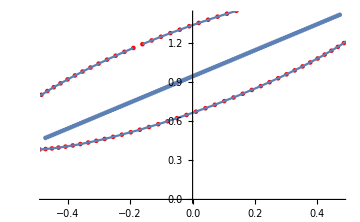
Natural | Binned
L^2 Error = 0.05906
-Graphics- | L^2 Error = 0.1776
-Graphics-

```mathematica
BinAnalysis[testData[1],$MTable,3]
```

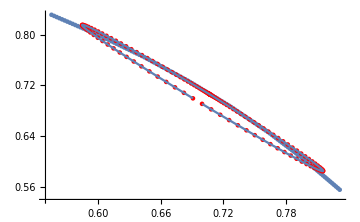
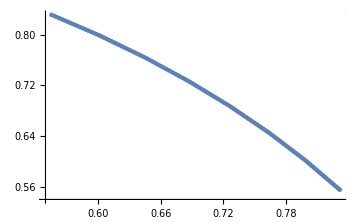
Natural | Binned
L^2 Error = 0.00309
-Graphics- | L^2 Error = 0.2495
-Graphics-

```mathematica
BinAnalysis[testData[2],$MTable,5]
```

```mathematica
(*Figure out how to to interpolation with normal Fourier coefficients first?*)
```